# Right-trivialized derivative dexp_X of the exp map on SE(3) The block-partitioning according to the semidirect product SE(3) = SO(3)⋉R.b3 is exploited

## References: [1]

## Verification of dexp_X and its first and second Fréchet derivatives

## Load package

```mathematica
AppendTo[$Path,"c:\\Users\\Andreas\\Research\\dexp\\SO3"];
AppendTo[$Path,"c:\\Users\\Andreas\\Research\\dexp\\SE3"];
```

```mathematica
<<"SE3PExp`"
```

## exp on SE(3)

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
```

```mathematica
SE3PExp[XX]//MatrixForm
```

(-0.312685 | 0.224802 | 0.922872 | 0.977859
0.937697 | 0.228025 | 0.262163 | 2.48334
-0.151503 | 0.947348 | -0.282096 | 0.0780562
0 | 0 | 0 | 1)

## dexp on SE(3)

## Check with analytic derivation

```mathematica
D0=D[se3ToTwist[Sum[D[SE3PExp[{x1,x2,x3,x4,x5,x6}],{x1,x2,x3,x4,x5,x6}[[ii]]]*{y1,y2,y3,y4,y5,y6}[[ii]],{ii,1,6}].SE3PExp[-{x1,x2,x3,x4,x5,x6}]],{{y1,y2,y3,y4,y5,y6}}]//Simplify;
```

```mathematica
D0diff=D0-SE3Pdexp[{x1,x2,x3,x4,x5,x6}];
D0diffEval[{x1_,x2_,x3_,x4_,x5_,x6_}]=D0diff;
```

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
D0diffEval[XX]//Norm
```

7.6885×10^-16

## Ddexp on SE(3)

## Check with analytic derivation

```mathematica
D1=D[SE3Pdexp[{x1,x2,x3,x4,x5,x6}],{{x1,x2,x3,x4,x5,x6}}].{y1,y2,y3,y4,y5,y6};
```

```mathematica
D1diffD1=D1-SE3PDdexp[{x1,x2,x3,x4,x5,x6},{y1,y2,y3,y4,y5,y6}];
D1diffEval[{x1_,x2_,x3_,x4_,x5_,x6_},{y1_,y2_,y3_,y4_,y5_,y6_}]=D1diffD1;
```

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
YY=Table[Random[Real,4],{ii,1,6}];
D1diffEval[XX,YY]//Norm
```

1.01534×10^-15

## Limit for x→0

```mathematica
LimD=Limit[D1,{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]
```

{{0,-y3/2,y2/2,0,0,0},{y3/2,0,-y1/2,0,0,0},{-y2/2,y1/2,0,0,0,0},{0,-y6/2,y5/2,0,-y3/2,y2/2},{y6/2,0,-y4/2,y3/2,0,-y1/2},{-y5/2,y4/2,0,-y2/2,y1/2,0}}

```mathematica
SE3PDdexp[{0,0,0,0,0,0},{y1,y2,y3,y4,y5,y6}]-LimD
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

## dexp^-1 on SE(3)

## Check by multiplication with dexp

```mathematica
xx=Table[Random[Real,4],{ii,1,6}];
SE3PdexpInv[xx].SE3Pdexp[xx]-IdentityMatrix[6]//Norm
```

1.35385×10^-15

## Ddexp^-1 on SE(3)

## Check with analytic derivation

```mathematica
D1Inv=D[SE3PdexpInv[{x1,x2,x3,x4,x5,x6}],{{x1,x2,x3,x4,x5,x6}}].{y1,y2,y3,y4,y5,y6}//Simplify;
```

```mathematica
D1InvdiffD1=D1Inv-SE3PDdexpInv[{x1,x2,x3,x4,x5,x6},{y1,y2,y3,y4,y5,y6}];
D1InvdiffEval[{x1_,x2_,x3_,x4_,x5_,x6_},{y1_,y2_,y3_,y4_,y5_,y6_}]=D1InvdiffD1;
```

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
YY=Table[Random[Real,4],{ii,1,6}];
D1InvdiffEval[XX,YY]//Norm
```

4.29679×10^-15

## Limit for x→0

```mathematica
LimDInv=Limit[D1Inv,{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]
```

{{0,y3/2,-y2/2,0,0,0},{-y3/2,0,y1/2,0,0,0},{y2/2,-y1/2,0,0,0,0},{0,y6/2,-y5/2,0,y3/2,-y2/2},{-y6/2,0,y4/2,-y3/2,0,y1/2},{y5/2,-y4/2,0,y2/2,-y1/2,0}}

```mathematica
SE3PDdexpInv[{0,0,0,0,0,0},{y1,y2,y3,y4,y5,y6}]-LimDInv//Simplify
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

# Right-trivialized derivative dexp_X of the exp map on SE(3) The adjoint 6x6 matrix representation is employed

## References: [1]

## Verification of dexp_X and its first and second Fréchet derivatives

## Load package

```mathematica
AppendTo[$Path,"c:\\Users\\Andreas\\Research\\dexp\\SE3"];
```

```mathematica
<<"SE3Exp`"
```

## exp

## Compare with the block-partitioned expression above

```mathematica
xx=Table[Random[Real,4],{ii,1,6}];
SE3Exp[xx].SE3PExp[-xx]-IdentityMatrix[4]//Norm
```

1.24343×10^-15

## dexp

## Compare with the block-partitioned expression above

```mathematica
xx=Table[Random[Real,4],{ii,1,6}];
SE3dexp[xx]-SE3Pdexp[xx]//Norm
```

6.9463×10^-16

## Limit X → 0

```mathematica
SE3dexp[xx*0]
```

{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}}

## dexp^-1

## Compare with the block-partitioned expression above

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
SE3dexpInv[XX]-SE3PdexpInv[XX]//Norm
```

8.97516×10^-16

## Limit X → 0

```mathematica
SE3dexpInv[XX*0]
```

{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}}

## Derivative of dexp

## Compare with the block-partitioned expression above

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
UU=Table[Random[Real,4],{ii,1,6}];
SE3Ddexp[XX,UU]-SE3PDdexp[XX,UU]//Norm
```

3.90858×10^-15

## Limit X → 0

```mathematica
SE3Ddexp[XX*0,UU]-SE3PDdexp[XX*0,UU]//Norm
```

0.

## Derivative of dexp^-1

## Compare with the block-partitioned expression above

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
UU=Table[Random[Real,4],{ii,1,6}];
SE3DdexpInv[XX,UU,-1]-SE3PDdexpInv[XX,UU]//Norm
```

5.32638×10^-15

## Limit X → 0

```mathematica
SE3DdexpInv[XX*0,UU]-SE3PDdexpInv[XX*0,UU]//Norm
```

0.

## Jacobian of dexp.Z

## Check with analytic derivation

```mathematica
adSE3dexpDiff[{x1_,x2_,x3_,y1_,y2_,y3_},{z1_,z2_,z3_,z4_,z5_,z6_}]=D[SE3dexp[{x1,x2,x3,y1,y2,y3}].{z1,z2,z3,z4,z5,z6},{{x1,x2,x3,y1,y2,y3}}];
```

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
ZZ=Table[Random[Real,4],{ii,1,6}];
adSE3dexpDiff[XX,ZZ]-SE3dexpJac[XX,ZZ,0]//Norm
```

2.45921×10^-15

## Limits for x → 0

```mathematica
SE3dexpJac[XX*0,ZZ]-Limit[adSE3dexpDiff[{x1,x2,x3,x4,x5,x6},ZZ],{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]
```

{{0.,0.,0.,0,0,0},{0.,0.,0.,0,0,0},{0.,0.,0.,0,0,0},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

## Jacobian of dexp^-1.Z

## Check with analytic derivation

```mathematica
adSE3dexpInvDiff[{x1_,x2_,x3_,y1_,y2_,y3_},{z1_,z2_,z3_,z4_,z5_,z6_}]=D[SE3dexpInv[{x1,x2,x3,y1,y2,y3}].{z1,z2,z3,z4,z5,z6},{{x1,x2,x3,y1,y2,y3}}];
```

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
ZZ=Table[Random[Real,4],{ii,1,6}];
adSE3dexpInvDiff[XX,ZZ]-SE3dexpInvJac[XX,ZZ]//Norm
```

1.0487×10^-14

## Limits for x → 0

```mathematica
SE3dexpInvJac[XX*0,ZZ]-Limit[adSE3dexpInvDiff[{x1,x2,x3,x4,x5,x6},ZZ],{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

## Jacobian of dexp^T.Z

## Check with analytic derivation

```mathematica
adSE3dexpTransposeDiff[{x1_,x2_,x3_,y1_,y2_,y3_},{z1_,z2_,z3_,z4_,z5_,z6_}]=D[Transpose[SE3dexp[{x1,x2,x3,y1,y2,y3}]].{z1,z2,z3,z4,z5,z6},{{x1,x2,x3,y1,y2,y3}}];
```

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
ZZ=Table[Random[Real,4],{ii,1,6}];
adSE3dexpTransposeDiff[XX,ZZ]-SE3dexpJacTranspose[XX,ZZ,0]//Norm
```

4.2197×10^-15

## Limits for x → 0

```mathematica
SE3dexpJacTranspose[XX*0,ZZ]-Limit[adSE3dexpTransposeDiff[{x1,x2,x3,x4,x5,x6},ZZ],{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0,0,0},{0.,0.,0.,0,0,0},{0.,0.,0.,0,0,0}}

## Derivative of Ddexp 2nd directional derivative of dexp

## Check with analytic derivation

```mathematica
adSE3D2dexp[{x1_,x2_,x3_,y1_,y2_,y3_},{u1_,u2_,u3_,u4_,u5_,u6_},{s1_,s2_,s3_,r1_,r2_,r3_}]=Sum[D[SE3PDdexp[{x1,x2,x3,y1,y2,y3},{u1,u2,u3,u4,u5,u6}],{x1,x2,x3,y1,y2,y3}[[ii]]]*{s1,s2,s3,r1,r2,r3}[[ii]],{ii,1,6}];
```

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
UU=Table[Random[Real,4],{ii,1,6}];
SS=Table[Random[Real,4],{ii,1,6}];
adSE3D2dexp[XX,UU,SS]-SE3D2dexp[XX,UU,SS]//Norm
```

8.36861×10^-14

## Limits for x → 0

```mathematica
SE3D2dexp[XX*0,UU,SS]-Limit[adSE3D2dexp[{x1,x2,x3,x4,x5,x6},UU,SS],{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]//Norm
```

1.22967×10^-15

## Derivative of Ddexp^-1 2nd directional derivative of dexp^-1

## Check with analytic derivation

```mathematica
adSE3D2dexpInv[{x1_,x2_,x3_,y1_,y2_,y3_},{u1_,u2_,u3_,u4_,u5_,u6_},{s1_,s2_,s3_,r1_,r2_,r3_}]=Sum[D[SE3PDdexpInv[{x1,x2,x3,y1,y2,y3},{u1,u2,u3,u4,u5,u6}],{x1,x2,x3,y1,y2,y3}[[ii]]]*{s1,s2,s3,r1,r2,r3}[[ii]],{ii,1,6}];
```

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
UU=Table[Random[Real,4],{ii,1,6}];
SS=Table[Random[Real,4],{ii,1,6}];
adSE3D2dexpInv[XX,UU,SS]-SE3D2dexpInv[XX,UU,SS]//Norm
```

4.29496×10^-14

## Limits for x → 0

```mathematica
SE3D2dexpInv[XX*0,UU,SS]-Limit[adSE3D2dexpInv[{x1,x2,x3,x4,x5,x6},UU,SS],{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]//Norm
```

4.97605×10^-16

## Hessian of Q^T.dexp.Z

## Check with analytic derivation

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
ZZ=Table[Random[Real,4],{ii,1,6}];
QQ=Table[Random[Real,4],{ii,1,6}];
```

```mathematica
adSE3dexpDiff2[{x1_,x2_,x3_,y1_,y2_,y3_},{q1_,q2_,q3_,q4_,q5_,q6_},{z1_,z2_,z3_,z4_,z5_,z6_}]=D[D[{q1,q2,q3,q4,q5,q6}.SE3dexp[{x1,x2,x3,y1,y2,y3}].{z1,z2,z3,z4,z5,z6},{{x1,x2,x3,y1,y2,y3}}],{{x1,x2,x3,y1,y2,y3}}];
```

```mathematica
SE3dexpHessian[XX,QQ,ZZ]-adSE3dexpDiff2[XX,QQ,ZZ]//Norm
```

2.45378×10^-14

## Limits for x → 0

```mathematica
HessianLim=Limit[SE3dexpHessian[{x1,x2,x3,x4,x5,x6},{q1,q2,q3,q4,q5,q6},{z1,z2,z3,z4,z5,z6}],{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]//Simplify
```

{{1/3 (-q2 z2-q3 z3-q5 z5-q6 z6),1/6 (q2 z1+q1 z2+q5 z4+q4 z5),1/6 (q3 z1+q1 z3+q6 z4+q4 z6),1/3 (-q5 z2-q6 z3),1/6 (q5 z1+q4 z2),1/6 (q6 z1+q4 z3)},{1/6 (q2 z1+q1 z2+q5 z4+q4 z5),1/3 (-q1 z1-q3 z3-q4 z4-q6 z6),1/6 (q3 z2+q2 z3+q6 z5+q5 z6),1/6 (q5 z1+q4 z2),1/3 (-q4 z1-q6 z3),1/6 (q6 z2+q5 z3)},{1/6 (q3 z1+q1 z3+q6 z4+q4 z6),1/6 (q3 z2+q2 z3+q6 z5+q5 z6),1/3 (-q1 z1-q2 z2-q4 z4-q5 z5),1/6 (q6 z1+q4 z3),1/6 (q6 z2+q5 z3),1/3 (-q4 z1-q5 z2)},{1/3 (-q5 z2-q6 z3),1/6 (q5 z1+q4 z2),1/6 (q6 z1+q4 z3),0,0,0},{1/6 (q5 z1+q4 z2),1/3 (-q4 z1-q6 z3),1/6 (q6 z2+q5 z3),0,0,0},{1/6 (q6 z1+q4 z3),1/6 (q6 z2+q5 z3),1/3 (-q4 z1-q5 z2),0,0,0}}

```mathematica
SE3dexpHessian[XX*0,{q1,q2,q3,q4,q5,q6},{z1,z2,z3,z4,z5,z6}]-HessianLim//Simplify
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

## Hessian of Q^T.dexp^-1.Z

### Check numerically

```mathematica
XX=Table[Random[Real,4],{ii,1,6}];
ZZ=Table[Random[Real,4],{ii,1,6}];
QQ=Table[Random[Real,4],{ii,1,6}];
```

```mathematica
adSE3dexpInvDiff2[{x1_,x2_,x3_,y1_,y2_,y3_},{q1_,q2_,q3_,q4_,q5_,q6_},{z1_,z2_,z3_,z4_,z5_,z6_}]=D[D[{q1,q2,q3,q4,q5,q6}.SE3dexpInv[{x1,x2,x3,y1,y2,y3}].{z1,z2,z3,z4,z5,z6},{{x1,x2,x3,y1,y2,y3}}],{{x1,x2,x3,y1,y2,y3}}];
```

```mathematica
SE3dexpInvHessian[XX,QQ,ZZ]-adSE3dexpInvDiff2[XX,QQ,ZZ]//Norm
```

1.46523×10^-14

## Limits for x → 0

```mathematica
HessianInvLim=Limit[SE3dexpInvHessian[{x1,x2,x3,x4,x5,x6},{q1,q2,q3,q4,q5,q6},{z1,z2,z3,z4,z5,z6}],{x1->0,x2->0,x3->0,x4->0,x5->0,x6->0}]//Simplify
```

{{1/6 (-q2 z2-q3 z3-q5 z5-q6 z6),1/12 (q2 z1+q1 z2+q5 z4+q4 z5),1/12 (q3 z1+q1 z3+q6 z4+q4 z6),1/6 (-q5 z2-q6 z3),1/12 (q5 z1+q4 z2),1/12 (q6 z1+q4 z3)},{1/12 (q2 z1+q1 z2+q5 z4+q4 z5),1/6 (-q1 z1-q3 z3-q4 z4-q6 z6),1/12 (q3 z2+q2 z3+q6 z5+q5 z6),1/12 (q5 z1+q4 z2),1/6 (-q4 z1-q6 z3),1/12 (q6 z2+q5 z3)},{1/12 (q3 z1+q1 z3+q6 z4+q4 z6),1/12 (q3 z2+q2 z3+q6 z5+q5 z6),1/6 (-q1 z1-q2 z2-q4 z4-q5 z5),1/12 (q6 z1+q4 z3),1/12 (q6 z2+q5 z3),1/6 (-q4 z1-q5 z2)},{1/6 (-q5 z2-q6 z3),1/12 (q5 z1+q4 z2),1/12 (q6 z1+q4 z3),0,0,0},{1/12 (q5 z1+q4 z2),1/6 (-q4 z1-q6 z3),1/12 (q6 z2+q5 z3),0,0,0},{1/12 (q6 z1+q4 z3),1/12 (q6 z2+q5 z3),1/6 (-q4 z1-q5 z2),0,0,0}}

```mathematica
SE3dexpInvHessian[XX*0,{q1,q2,q3,q4,q5,q6},{z1,z2,z3,z4,z5,z6}]-HessianInvLim//Simplify
```

{{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

# Higher-Order Approximations in terms of the adjoint 6x6 matrix representation

## Investigate the approximation order by means of examples

## Helper function to generate input for ListPlot

```mathematica
MakePlotData[xDat_,yDat_]:=MapThread[Flatten@*List,{xDat,#}]&/@yDat;
```

## dexp

## Specific (but random) values for Xn

```mathematica
e={0.3,-0.4,1};
en=e/Norm[e];
Xn=Join[en,{0.1,0.2,-0.4}]
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

## Compare 1st-, ... , 4th-order approximations with exact values

```mathematica
tmax=1*^-1;
nTab=1000;
```

```mathematica
epsX=1*^-12;
```

```mathematica
dexpTab1=Table[Norm[SE3dexp[Xn*tt,epsX]-SE3dexpOrder1[Xn*tt]],{tt,0,tmax,tmax/nTab}];
dexpTab2=Table[Norm[SE3dexp[Xn*tt,epsX]-SE3dexpOrder2[Xn*tt]],{tt,0,tmax,tmax/nTab}];
dexpTab3=Table[Norm[SE3dexp[Xn*tt,epsX]-SE3dexpOrder3[Xn*tt]],{tt,0,tmax,tmax/nTab}];
dexpTab4=Table[Norm[SE3dexp[Xn*tt,epsX]-SE3dexpOrder4[Xn*tt]],{tt,0,tmax,tmax/nTab}];
```

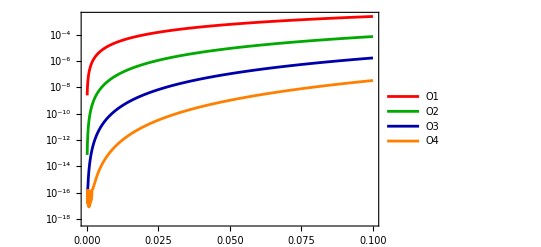

```mathematica
ListLogPlot[MakePlotData[Table[tt,{tt,0,tmax,tmax/nTab}],{dexpTab1,dexpTab2,dexpTab3,dexpTab4}],Frame->True,Joined->True,PlotStyle->{Red,Darker[Green],Darker[Blue],Orange},PlotLegends->{"O1","O2","O3","O4"}]
```

## dexp^-1

## Specific (but random) values for Xn

```mathematica
e={0.3,-0.4,1};
en=e/Norm[e];
Xn=Join[en,{0.1,0.2,-0.4}]
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

## Compare 1st-, ... , 4th-order approximations with exact values

```mathematica
tmax=1*^-1;
nTab=1000;
```

```mathematica
epsX=1*^-12;
```

```mathematica
dexpInvTab1=Table[Norm[SE3dexpInv[Xn*tt,epsX]-SE3dexpInvOrder1[Xn*tt]],{tt,0,tmax,tmax/nTab}];
dexpInvTab2=Table[Norm[SE3dexpInv[Xn*tt,epsX]-SE3dexpInvOrder2[Xn*tt]],{tt,0,tmax,tmax/nTab}];
dexpInvTab4=Table[Norm[SE3dexpInv[Xn*tt,epsX]-SE3dexpInvOrder4[Xn*tt]],{tt,0,tmax,tmax/nTab}];
```

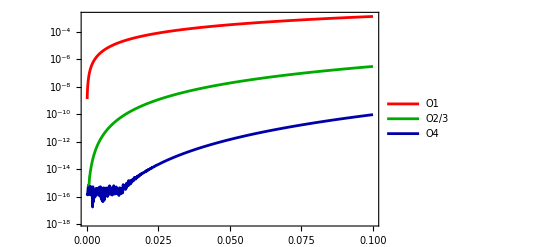

```mathematica
ListLogPlot[MakePlotData[Table[tt,{tt,0,tmax,tmax/nTab}],{dexpInvTab1,dexpInvTab2,dexpInvTab4}],Frame->True,Joined->True,PlotStyle->{Red,Darker[Green],Darker[Blue]},PlotLegends->{"O1","O2/3","O4"}]
```

## Ddexp

## Specific (but random) values for Xn

```mathematica
e={0.3,-0.4,1};
en=e/Norm[e];
Xn=Join[en,{0.1,0.2,-0.4}]
Utest={0.1,1.0,-1.0,0.9,0.5,0.3}
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

{0.1,1.,-1.,0.9,0.5,0.3}

## Compare 0th-, ... , 3rd-order approximations with exact values

```mathematica
tmax=1*^-1;
nTab=1000;
```

```mathematica
epsX=1*^-12;
```

```mathematica
DdexpTab0=Table[Norm[SE3Ddexp[Xn*tt,Utest,epsX]-SE3DdexpOrder0[Xn*tt,Utest]],{tt,0,tmax,tmax/nTab}];
DdexpTab1=Table[Norm[SE3Ddexp[Xn*tt,Utest,epsX]-SE3DdexpOrder1[Xn*tt,Utest]],{tt,0,tmax,tmax/nTab}];
DdexpTab2=Table[Norm[SE3Ddexp[Xn*tt,Utest,epsX]-SE3DdexpOrder2[Xn*tt,Utest]],{tt,0,tmax,tmax/nTab}];
DdexpTab3=Table[Norm[SE3Ddexp[Xn*tt,Utest,epsX]-SE3DdexpOrder3[Xn*tt,Utest]],{tt,0,tmax,tmax/nTab}];
```

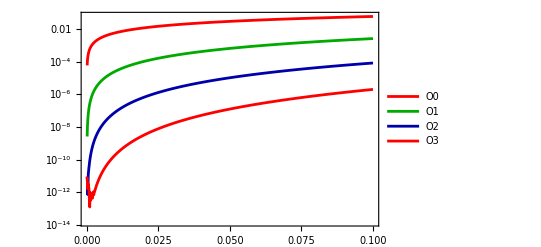

```mathematica
ListLogPlot[MakePlotData[Table[tt,{tt,0,tmax,tmax/nTab}],{DdexpTab0,DdexpTab1,DdexpTab2,DdexpTab3}],Frame->True,Joined->True,PlotStyle->{Red,Darker[Green],Darker[Blue]},PlotLegends->{"O0","O1","O2","O3"}]
```

## Ddexp^-1

## Specific (but random) values for Xn

```mathematica
e={0.3,-0.4,1};
en=e/Norm[e];
Xn=Join[en,{0.1,0.2,-0.4}]
Utest={0.1,1.0,-1.0,0.9,0.5,0.3}
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

{0.1,1.,-1.,0.9,0.5,0.3}

## Compare 0th-, ... , 3rd-order approximations with exact values

```mathematica
tmax=1*^-1;
nTab=1000;
```

```mathematica
epsX=1*^-12;
```

```mathematica
DdexpInvTab0=Table[Norm[SE3DdexpInv[Xn*tt,Utest,epsX]-SE3DdexpInvOrder0[Xn*tt,Utest]],{tt,0,tmax,tmax/nTab}];
DdexpInvTab1=Table[Norm[SE3DdexpInv[Xn*tt,Utest,epsX]-SE3DdexpInvOrder1[Xn*tt,Utest]],{tt,0,tmax,tmax/nTab}];
DdexpInvTab2=Table[Norm[SE3DdexpInv[Xn*tt,Utest,epsX]-SE3DdexpInvOrder2[Xn*tt,Utest]],{tt,0,tmax,tmax/nTab}];
DdexpInvTab3=Table[Norm[SE3DdexpInv[Xn*tt,Utest,epsX]-SE3DdexpInvOrder3[Xn*tt,Utest]],{tt,0,tmax,tmax/nTab}];
```

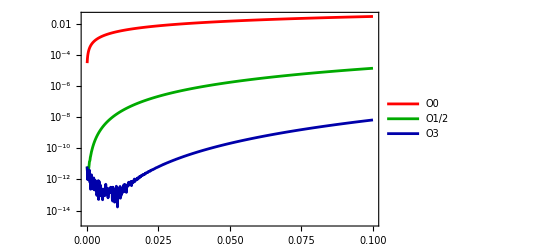

```mathematica
ListLogPlot[MakePlotData[Table[tt,{tt,0,tmax,tmax/nTab}],{DdexpInvTab0,DdexpInvTab1,DdexpInvTab3}],Frame->True,Joined->True,PlotStyle->{Red,Darker[Green],Darker[Blue]},PlotLegends->{"O0","O1/2","O3"}]
```

## D2dexp

## Specific (but random) values for Xn

```mathematica
e={0.3,-0.4,1};
en=e/Norm[e];
Xn=Join[en,{0.1,0.2,-0.4}]
Utest={0.1,1.0,-1.0,0.9,0.5,0.3}
Stest={1.7,-2.9,-9.2,7.6,6.7,2.4};
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

{0.1,1.,-1.,0.9,0.5,0.3}

## Compare 0th-, ... ,2nd-order approximations with exact values

```mathematica
tmax=1*^-1;
nTab=1000;
```

```mathematica
epsX=1*^-12;
```

```mathematica
D2dexpTab0=Table[Norm[SE3D2dexp[Xn*tt,Utest,Stest,epsX]-SE3D2dexpOrder0[Xn*tt,Utest,Stest]],{tt,0,tmax,tmax/nTab}];
D2dexpTab1=Table[Norm[SE3D2dexp[Xn*tt,Utest,Stest,epsX]-SE3D2dexpOrder1[Xn*tt,Utest,Stest]],{tt,0,tmax,tmax/nTab}];
D2dexpTab2=Table[Norm[SE3D2dexp[Xn*tt,Utest,Stest,epsX]-SE3D2dexpOrder2[Xn*tt,Utest,Stest]],{tt,0,tmax,tmax/nTab}];
```

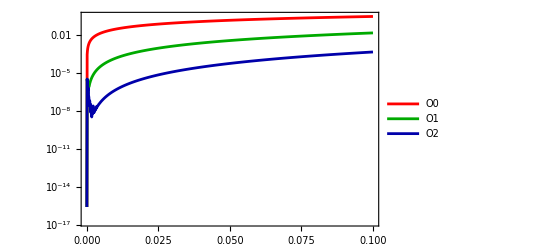

```mathematica
pl12=ListLogPlot[MakePlotData[Table[tt,{tt,0,tmax,tmax/nTab}],{D2dexpTab0,D2dexpTab1,D2dexpTab2}],Frame->True,Joined->True,PlotStyle->{Red,Darker[Green],Darker[Blue]},FrameStyle->Black,PlotLegends->{"O0","O1","O2"}]
```

## D2dexp^-1

## Specific (but random) values for Xn

```mathematica
e={0.3,-0.4,1};
en=e/Norm[e];
Xn=Join[en,{0.1,0.2,-0.4}]
Utest={0.1,1.0,-1.0,0.9,0.5,0.3}
Stest={1.7,-2.9,-9.2,7.6,6.7,2.4};
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

{0.1,1.,-1.,0.9,0.5,0.3}

## Compare 0th-, ... ,2nd-order approximations with exact values

```mathematica
tmax=1*^-1;
nTab=1000;
```

```mathematica
epsX=1*^-12;
```

```mathematica
D2dexpInvTab0=Table[Norm[SE3D2dexpInv[Xn*tt,Utest,Stest,epsX]-SE3D2dexpInvOrder0[Xn*tt,Utest,Stest]],{tt,0,tmax,tmax/nTab}];
D2dexpInvTab2=Table[Norm[SE3D2dexpInv[Xn*tt,Utest,Stest,epsX]-SE3D2dexpInvOrder2[Xn*tt,Utest,Stest]],{tt,0,tmax,tmax/nTab}];
```

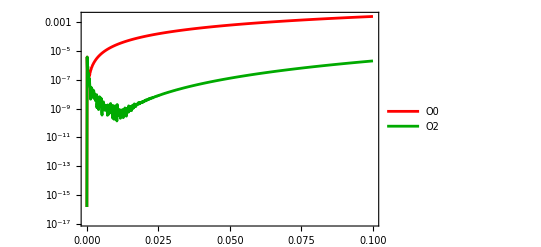

```mathematica
ListLogPlot[MakePlotData[Table[tt,{tt,0,tmax,tmax/nTab}],{D2dexpInvTab0,D2dexpInvTab2}],Frame->True,Joined->True,PlotStyle->{Red,Darker[Green]},FrameStyle->Black,PlotLegends->{"O0","O2"}]
```

## Jacobian of dexp.Z

## Specific (but random) values for Xn

```mathematica
e={0.3,-0.4,1};
en=e/Norm[e];
Xn=Join[en,{0.1,0.2,-0.4}]
Ztest={0.1,1.0,-1.0,0.9,0.5,0.3}
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

{0.1,1.,-1.,0.9,0.5,0.3}

## Compare 0th-, ... ,2nd-order approximations with exact values

```mathematica
tmax=1*^-1;
nTab=1000;
```

```mathematica
epsX=1*^-12;
```

```mathematica
JacTab0=Table[Norm[SE3dexpJac[Xn*tt,Ztest,epsX]-SE3dexpJacOrder0[Xn*tt,Ztest]],{tt,0,tmax,tmax/nTab}];
JacTab1=Table[Norm[SE3dexpJac[Xn*tt,Ztest,epsX]-SE3dexpJacOrder1[Xn*tt,Ztest]],{tt,0,tmax,tmax/nTab}];
JacTab2=Table[Norm[SE3dexpJac[Xn*tt,Ztest,epsX]-SE3dexpJacOrder2[Xn*tt,Ztest]],{tt,0,tmax,tmax/nTab}];
```

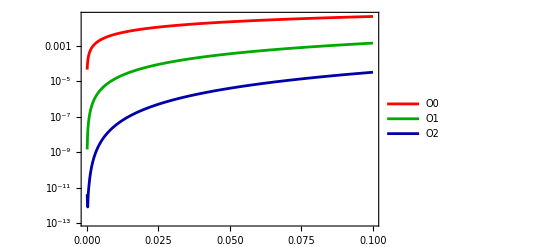

```mathematica
ListLogPlot[MakePlotData[Table[tt,{tt,0,tmax,tmax/nTab}],{JacTab0,JacTab1,JacTab2}],Frame->True,Joined->True,PlotStyle->{Red,Darker[Green],Darker[Blue]},FrameStyle->Black,PlotLegends->{"O0","O1","O2"}]
```

## Hessian of Q^T.dexp.Z

## Specific (but random) values for Xn

```mathematica
e={0.3,-0.4,1};
en=e/Norm[e];
Xn=Join[en,{0.1,0.2,-0.4}]
Ztest={0.1,1.0,-1.0,0.9,0.5,0.3}
Qtest={1.7,-2.9,-9.2,7.6,6.7,2.4}
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

{0.1,1.,-1.,0.9,0.5,0.3}

{1.7,-2.9,-9.2,7.6,6.7,2.4}

## Compare 0th-, ... ,2nd-order approximations with exact values

```mathematica
tmax=1*^-1;
nTab=1000;
```

```mathematica
epsX=1*^-12;
```

#### Well-defined values for Xn, Z, Q:

```mathematica
en={0.3,-0.4,1};
en=en/Norm[en];
Xn=Join[en,{0.1,0.2,-0.4}]
```

{0.268328,-0.357771,0.894427,0.1,0.2,-0.4}

```mathematica
HessianTab0=Table[Norm[SE3dexpHessian[Xn*tt,Qtest,Ztest,epsX]-SE3dexpHessianOrder0[Xn*tt,Qtest,Ztest]],{tt,0,tmax,tmax/nTab}];
HessianTab1=Table[Norm[SE3dexpHessian[Xn*tt,Qtest,Ztest,epsX]-SE3dexpHessianOrder1[Xn*tt,Qtest,Ztest]],{tt,0,tmax,tmax/nTab}];
HessianTab2=Table[Norm[SE3dexpHessian[Xn*tt,Qtest,Ztest,epsX]-SE3dexpHessianOrder2[Xn*tt,Qtest,Ztest]],{tt,0,tmax,tmax/nTab}];
```

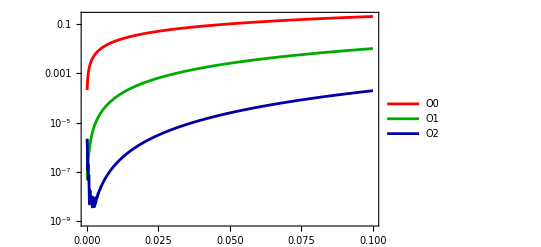

```mathematica
ListLogPlot[MakePlotData[Table[tt,{tt,0,tmax,tmax/nTab}],{HessianTab0,HessianTab1,HessianTab2}],Frame->True,Joined->True,PlotStyle->{Red,Darker[Green],Darker[Blue]},FrameStyle->Black,PlotLegends->{"O0","O1","O2"}]
```